```mathematica
d=2;
n=11;
```

```mathematica
e[n_]:=e[n]=Table[1,{i,n}]
r[n_]:=r[n]=Table[(i-1),{i,n}]
```

```mathematica
W2[n_]:=W2[n]=DiagonalMatrix[Table[If[i==1,1/2,1],{i,n}]]
W4[n_]:=W4[n]=DiagonalMatrix[Table[If[i==1,1/2,1],{i,n}]]
W6[n_]:=W6[n]=DiagonalMatrix[Table[If[i==1,1/2,1],{i,n}]]
W8[n_]:=W8[n]=DiagonalMatrix[Table[If[i==1,1/2,1],{i,n}]]
W8[n]//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
B2[n_]:=B2[n]=DiagonalMatrix[Table[0,{i,n}]]
B4[n_]:=B4[n]=DiagonalMatrix[Table[0,{i,n}]]
B6[n_]:=B6[n]=DiagonalMatrix[Table[0,{i,n}]]
B8[n_]:=B8[n]=DiagonalMatrix[Table[0,{i,n}]]
B8[n]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
s2[i_]:=If[Abs[i]<=1,{-1/2,0,1/2}[[i+2]],0]
s4n[i_]:=If[Abs[i]<=2,{0,-1/2,0,1/2,0}[[i+3]],0]
s4w[i_]:=If[Abs[i]<=2,{-1/4,0,0,0,1/4}[[i+3]],0]
s6a[i_]:=If[Abs[i]<=3,{0,0,-1/2,0,1/2,0,0}[[i+4]],0]
s6b[i_]:=If[Abs[i]<=3,{0,-1/4,0,0,0,1/4,0}[[i+4]],0]
s6c[i_]:=If[Abs[i]<=3,{-1/6,0,0,0,0,0,1/6}[[i+4]],0]
s8a[i_]:=If[Abs[i]<=4,{0,0,0,-1/2,0,1/2,0,0,0}[[i+5]],0]
s8b[i_]:=If[Abs[i]<=4,{0,0,-1/4,0,0,0,1/4,0,0}[[i+5]],0]
s8c[i_]:=If[Abs[i]<=4,{0,-1/6,0,0,0,0,0,1/6,0}[[i+5]],0]
s8d[i_]:=If[Abs[i]<=4,{-1/8,0,0,0,0,0,0,0,1/8}[[i+5]],0]
Grad2[n_]:=Grad2[n]=Table[If[j==1,1/2,1](s2[j-i]+s2[-i-j+2]),{i,n},{j,n}]
Grad4n[n_]:=Grad4n[n]=Table[If[j==1,1/2,1](s4n[j-i]+s4n[-i-j+2]),{i,n},{j,n}]
Grad4w[n_]:=Grad4w[n]=Table[If[j==1,1/2,1](s4w[j-i]+s4w[-i-j+2]),{i,n},{j,n}]
Grad4[n_]:=Grad4[n]=4/3Grad4n[n]-1/3Grad4w[n]
Grad6a[n_]:=Grad6a[n]=Table[If[j==1,1/2,1](s6a[j-i]+s6a[-i-j+2]),{i,n},{j,n}]
Grad6b[n_]:=Grad6b[n]=Table[If[j==1,1/2,1](s6b[j-i]+s6b[-i-j+2]),{i,n},{j,n}]
Grad6c[n_]:=Grad6c[n]=Table[If[j==1,1/2,1](s6c[j-i]+s6c[-i-j+2]),{i,n},{j,n}]
Grad6[n_]:=Grad6[n]=3/2Grad6a[n]-3/5Grad6b[n]+1/10Grad6c[n]
Grad8a[n_]:=Grad8a[n]=Table[If[j==1,1/2,1](s8a[j-i]+s8a[-i-j+2]),{i,n},{j,n}]
Grad8b[n_]:=Grad8b[n]=Table[If[j==1,1/2,1](s8b[j-i]+s8b[-i-j+2]),{i,n},{j,n}]
Grad8c[n_]:=Grad8c[n]=Table[If[j==1,1/2,1](s8c[j-i]+s8c[-i-j+2]),{i,n},{j,n}]
Grad8d[n_]:=Grad8d[n]=Table[If[j==1,1/2,1](s8d[j-i]+s8d[-i-j+2]),{i,n},{j,n}]
Grad8[n_]:=Grad8[n]=8/5Grad8a[n]-4/5Grad8b[n]+8/35Grad8c[n]-1/35Grad8d[n]
Grad8[n]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4/5 | 1/5 | 16/21 | -11/56 | 4/105 | -1/280 | 0 | 0 | 0 | 0 | 0
1/5 | -88/105 | 1/280 | 4/5 | -1/5 | 4/105 | -1/280 | 0 | 0 | 0 | 0
-4/105 | 57/280 | -4/5 | 0 | 4/5 | -1/5 | 4/105 | -1/280 | 0 | 0 | 0
1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5 | 4/105 | -1/280 | 0 | 0
0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5 | 4/105 | -1/280 | 0
0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5 | 4/105 | -1/280
0 | 0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5 | 4/105
0 | 0 | 0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5
0 | 0 | 0 | 0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5
0 | 0 | 0 | 0 | 0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0)

```mathematica
Grad2[n].e[n]
Grad4n[n].e[n]
Grad4n[n].r[n]^2-2r[n]
Grad4w[n].e[n]
Grad4w[n].r[n]^2-2r[n]
Grad4[n].e[n]
Grad4[n].r[n]^2-2r[n]
Grad4[n].r[n]^4-4r[n]^3
Grad6a[n].e[n]
Grad6a[n].r[n]^2-2r[n]
Grad6b[n].e[n]
Grad6b[n].r[n]^2-2r[n]
Grad6c[n].e[n]
Grad6c[n].r[n]^2-2r[n]
Grad6[n].e[n]
Grad6[n].r[n]^2-2r[n]
Grad6[n].r[n]^4-4r[n]^3
Grad6[n].r[n]^6-6r[n]^5
Grad8a[n].e[n]
Grad8a[n].r[n]^2-2r[n]
Grad8b[n].e[n]
Grad8b[n].r[n]^2-2r[n]
Grad8c[n].e[n]
Grad8c[n].r[n]^2-2r[n]
Grad8d[n].e[n]
Grad8d[n].r[n]^2-2r[n]
Grad8[n].e[n]
Grad8[n].r[n]^2-2r[n]
Grad8[n].r[n]^4-4r[n]^3
Grad8[n].r[n]^6-6r[n]^5
Grad8[n].r[n]^8-8r[n]^7
```

{0,0,0,0,0,0,0,0,0,0,-1/2}

{0,0,0,0,0,0,0,0,0,0,-1/2}

{0,0,0,0,0,0,0,0,0,0,-121/2}

{0,0,0,0,0,0,0,0,0,-1/4,-1/4}

{0,0,0,0,0,0,0,0,0,-121/4,-36}

{0,0,0,0,0,0,0,0,0,1/12,-7/12}

{0,0,0,0,0,0,0,0,0,121/12,-206/3}

{0,0,0,0,0,0,0,0,0,14641/12,-24098/3}

{0,0,0,0,0,0,0,0,0,0,-1/2}

{0,0,0,0,0,0,0,0,0,0,-121/2}

{0,0,0,0,0,0,0,0,0,-1/4,-1/4}

{0,0,0,0,0,0,0,0,0,-121/4,-36}

{0,0,0,0,0,0,0,0,-1/6,-1/6,-1/6}

{0,0,0,0,0,0,0,0,-121/6,-24,-169/6}

{0,0,0,0,0,0,0,0,-1/60,2/15,-37/60}

{0,0,0,0,0,0,0,0,-121/60,63/4,-2159/30}

{0,0,0,0,0,0,0,0,-14641/60,37011/20,-250391/30}

{0,0,0,0,0,0,0,0,-1771561/60,863871/4,-28836599/30}

{0,0,0,0,0,0,0,0,0,0,-1/2}

{0,0,0,0,0,0,0,0,0,0,-121/2}

{0,0,0,0,0,0,0,0,0,-1/4,-1/4}

{0,0,0,0,0,0,0,0,0,-121/4,-36}

{0,0,0,0,0,0,0,0,-1/6,-1/6,-1/6}

{0,0,0,0,0,0,0,0,-121/6,-24,-169/6}

{0,0,0,0,0,0,0,-1/8,-1/8,-1/8,-1/8}

{0,0,0,0,0,0,0,-121/8,-18,-169/8,-49/2}

{0,0,0,0,0,0,0,1/280,-29/840,139/840,-533/840}

{0,0,0,0,0,0,0,121/280,-86/21,5409/280,-3097/42}

{0,0,0,0,0,0,0,14641/280,-50788/105,627273/280,-894226/105}

{0,0,0,0,0,0,0,1771561/280,-1193300/21,72183729/280,-20517824/21}

{0,0,0,0,0,0,0,214358881/280,-696192388/105,8233356633/280,-11686032376/105}

```mathematica
V2[n_]:=V2[n]=W2[n]
V4[n_]:=V4[n]=W4[n]
V6[n_]:=V6[n]=W6[n]
V8[n_]:=V8[n]=W8[n]
```

```mathematica
(* V.Grad + (W.Div)' = B *)
```

```mathematica
Div2[n_]:=Div2[n]=Inverse[W2[n]].Transpose[B2[n]-V2[n].Grad2[n]]
Div4n[n_]:=Div4n[n]=Inverse[W4[n]].Transpose[B4[n]-V4[n].Grad4n[n]]
Div4w[n_]:=Div4w[n]=Inverse[W4[n]].Transpose[B4[n]-V4[n].Grad4w[n]]
Div4[n_]:=Div4[n]=4/3Div4n[n]-1/3Div4w[n]
Div6a[n_]:=Div6a[n]=Inverse[W6[n]].Transpose[B6[n]-V6[n].Grad6a[n]]
Div6b[n_]:=Div6b[n]=Inverse[W6[n]].Transpose[B6[n]-V6[n].Grad6b[n]]
Div6c[n_]:=Div6c[n]=Inverse[W6[n]].Transpose[B6[n]-V6[n].Grad6c[n]]
Div6[n_]:=Div6[n]=3/2Div6a[n]-3/5Div6b[n]+1/10Div6c[n]
Div8a[n_]:=Div8a[n]=Inverse[W8[n]].Transpose[B8[n]-V8[n].Grad8a[n]]
Div8b[n_]:=Div8b[n]=Inverse[W8[n]].Transpose[B8[n]-V8[n].Grad8b[n]]
Div8c[n_]:=Div8c[n]=Inverse[W8[n]].Transpose[B8[n]-V8[n].Grad8c[n]]
Div8d[n_]:=Div8d[n]=Inverse[W8[n]].Transpose[B8[n]-V8[n].Grad8d[n]]
Div8[n_]:=Div8[n]=8/5Div8a[n]-4/5Div8b[n]+8/35Div8c[n]-1/35Div8d[n]
Div8[n]//MatrixForm
```

(0 | 8/5 | -2/5 | 8/105 | -1/140 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/5 | 88/105 | -57/280 | 4/105 | -1/280 | 0 | 0 | 0 | 0 | 0
0 | -16/21 | -1/280 | 4/5 | -1/5 | 4/105 | -1/280 | 0 | 0 | 0 | 0
0 | 11/56 | -4/5 | 0 | 4/5 | -1/5 | 4/105 | -1/280 | 0 | 0 | 0
0 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5 | 4/105 | -1/280 | 0 | 0
0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5 | 4/105 | -1/280 | 0
0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5 | 4/105 | -1/280
0 | 0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5 | 4/105
0 | 0 | 0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5 | -1/5
0 | 0 | 0 | 0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0 | 4/5
0 | 0 | 0 | 0 | 0 | 0 | 1/280 | -4/105 | 1/5 | -4/5 | 0)

```mathematica
Div2[n].r[n]-e[n]
Div4n[n].r[n]-e[n]
Div4w[n].r[n]-e[n]
Div4[n].r[n]-e[n]
Div4[n].r[n]^3-3r[n]^2
Div6a[n].r[n]-e[n]
Div6b[n].r[n]-e[n]
Div6c[n].r[n]-e[n]
Div6[n].r[n]-e[n]
Div6[n].r[n]^3-3r[n]^2
Div6[n].r[n]^5-5r[n]^4
Div8a[n].r[n]-e[n]
Div8b[n].r[n]-e[n]
Div8c[n].r[n]-e[n]
Div8d[n].r[n]-e[n]
Div8[n].r[n]-e[n]
Div8[n].r[n]^3-3r[n]^2
Div8[n].r[n]^5-5r[n]^4
Div8[n].r[n]^7-7r[n]^6
```

{0,0,0,0,0,0,0,0,0,0,-11/2}

{0,0,0,0,0,0,0,0,0,0,-11/2}

{0,0,0,0,0,0,0,0,0,-11/4,-3}

{0,0,0,0,0,0,0,0,0,11/12,-19/3}

{0,0,0,0,0,0,0,0,0,1331/12,-2230/3}

{0,0,0,0,0,0,0,0,0,0,-11/2}

{0,0,0,0,0,0,0,0,0,-11/4,-3}

{0,0,0,0,0,0,0,0,-11/6,-2,-13/6}

{0,0,0,0,0,0,0,0,-11/60,29/20,-20/3}

{0,0,0,0,0,0,0,0,-1331/60,3417/20,-2327/3}

{0,0,0,0,0,0,0,0,-161051/60,400209/20,-268955/3}

{0,0,0,0,0,0,0,0,0,0,-11/2}

{0,0,0,0,0,0,0,0,0,-11/4,-3}

{0,0,0,0,0,0,0,0,-11/6,-2,-13/6}

{0,0,0,0,0,0,0,-11/8,-3/2,-13/8,-7/4}

{0,0,0,0,0,0,0,11/280,-79/210,501/280,-575/84}

{0,0,0,0,0,0,0,1331/280,-668/15,58301/280,-16655/21}

{0,0,0,0,0,0,0,161051/280,-550892/105,6735941/280,-1917260/21}

{0,0,0,0,0,0,0,19487171/280,-64511756/105,771824141/280,-219183680/21}

```mathematica
(*(R2=h^2DiagonalMatrix[Table[(i-1)^2,{i,n}]])//MatrixForm*)
```

```mathematica
R22[d_,n_]:=R22[d,n]=DiagonalMatrix[Table[a[i-1],{i,n}]]
Assert[R22[d,n]==Transpose[R22[d,n]]];
R24n[d_,n_]:=R24n[d,n]=(DiagonalMatrix[Table[a[i-1],{i,n}]]+SparseArray[{{1,2}->a[0,1],{2,1}->a[0,1],{1,3}->a[0,2],{3,1}->a[0,2],{2,3}->a[1,2],{3,2}->a[1,2]},n])
R24w[d_,n_]:=R24w[d,n]=DiagonalMatrix[Table[b[i-1],{i,n}]]
Assert[R24n[d,n]==Transpose[R24n[d,n]]];
Assert[R24w[d,n]==Transpose[R24w[d,n]]];
R26a[n_]:=R26a[n]=(DiagonalMatrix[Table[a[i-1],{i,n}]]+SparseArray[{{1,2}->a[0,1],{2,1}->a[0,1],{1,3}->a[0,2],{3,1}->a[0,2],{2,3}->a[1,2],{3,2}->a[1,2]},n])
R26b[n_]:=R26b[n]=DiagonalMatrix[Table[b[i-1],{i,n}]]
R26c[n_]:=R26c[n]=DiagonalMatrix[Table[c[i-1],{i,n}]]
Assert[R26a[n]==Transpose[R26a[n]]];
Assert[R26b[n]==Transpose[R26b[n]]];
Assert[R26c[n]==Transpose[R26c[n]]];
R28a[n_]:=R28a[n]=(DiagonalMatrix[Table[a[i-1],{i,n}]]+SparseArray[{{1,2}->a[0,1],{2,1}->a[0,1],{1,3}->a[0,2],{3,1}->a[0,2],{2,3}->a[1,2],{3,2}->a[1,2]},n])
R28b[n_]:=R28b[n]=DiagonalMatrix[Table[b[i-1],{i,n}]]
R28c[n_]:=R28c[n]=DiagonalMatrix[Table[c[i-1],{i,n}]]
R28d[n_]:=R28d[n]=DiagonalMatrix[Table[d[i-1],{i,n}]]
Assert[R28a[n]==Transpose[R28a[n]]];
Assert[R28b[n]==Transpose[R28b[n]]];
Assert[R28c[n]==Transpose[R28c[n]]];
Assert[R28d[n]==Transpose[R28d[n]]];
R24n[3,n]//MatrixForm
```

(a[0] | a[0,1] | a[0,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a[0,1] | a[1] | a[1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a[0,2] | a[1,2] | a[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a[4] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a[5] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a[6] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a[7] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a[8] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a[9] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a[10])

```mathematica
(* R2.V.Grad + (W.R2.Inverse[R2].Div.R2)' = R2.B *)
```

#### Solve p=2

```mathematica
conds2[d_,n_]:=(*conds2[d,n]=*)(Div2[n].R22[d,n].r[n]-R22[d,n].(d e[n]))//Simplify
conds2[d,n]//MatrixForm
```

(-2 a[0]+a[1]
-2 a[1]+a[2]
1/2 (-a[1]-4 a[2]+3 a[3])
-a[2]-2 a[3]+2 a[4]
1/2 (-3 a[3]-4 a[4]+5 a[5])
-2 a[4]-2 a[5]+3 a[6]
1/2 (-5 a[5]-4 a[6]+7 a[7])
-3 a[6]-2 a[7]+4 a[8]
1/2 (-7 a[7]-4 a[8]+9 a[9])
-4 a[8]-2 a[9]+5 a[10]
-(9 a[9])/2-2 a[10])

```mathematica
qval2[d_,n_]:={0,0,1/2,2(n-1),3/2+5(n-1)^2,23/2(n-1)+10(n-1)^3}[[d]]
sol2[d_,n_]:=(*sol2[d,n]=*)Solve[Join[conds2[d,n][[1;;n-1]],Table[a[n-i]-((n-i)^(d-1)+q[i]),{i,1,1}],{q[1]-qval2[d,n]}]==0,Join[Table[a[i-1],{i,n}],{q[1]}]][[1]];
sol2[d,n]//Expand//MatrixForm
```

(a[0]→1/2
a[1]→1
a[2]→2
a[3]→3
a[4]→4
a[5]→5
a[6]→6
a[7]→7
a[8]→8
a[9]→9
a[10]→10
q[1]→0)

```mathematica
Solve[(a[0]/.sol2[d,n])==(a[0]/.sol2[d,n+1])]
```

{{}}

```mathematica
R22[d,n]/.sol2[d,n]//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10)

```mathematica
SDiv2[d_,n_]:=(*SDiv2[d,n]=*)Inverse[R22[d,n]].Div2[n].R22[d,n]/.sol2[d,n]
SDiv2[d,n]//MatrixForm
```

(0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/4 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/3 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -3/8 | 0 | 5/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2/5 | 0 | 3/5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -5/12 | 0 | 7/12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3/7 | 0 | 4/7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -7/16 | 0 | 9/16 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/9 | 0 | 5/9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9/20 | 0)

```mathematica
SDiv2[d,n].r[n]-d e[n]
```

{0,0,0,0,0,0,0,0,0,0,-121/20}

```mathematica
(vals2=Eigenvalues[SDiv2[d,n]])//MatrixForm;
```

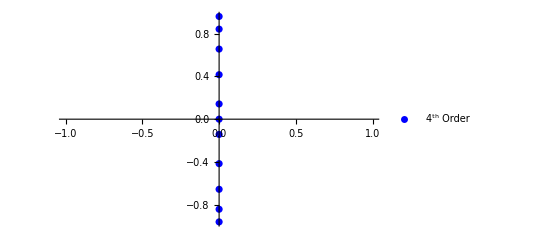

```mathematica
cplot2=ComplexListPlot[vals2,AspectRatio->1/GoldenRatio, PlotStyle->Blue, PlotLegends->{"4^th Order"},PlotRange->All]
```

#### Solve p=4

```mathematica
conds4w[d_,n_]:=(*conds4w[d,n]=*)(Div4w[n].R24w[d,n].r[n]-R24w[d,n] .(d e[n]))//Simplify
conds4w[d,n]//MatrixForm
```

(-2 b[0]+b[2]
1/4 (-7 b[1]+3 b[3])
-2 b[2]+b[4]
1/4 (-b[1]-8 b[3]+5 b[5])
1/2 (-b[2]-4 b[4]+3 b[6])
1/4 (-3 b[3]-8 b[5]+7 b[7])
-b[4]-2 b[6]+2 b[8]
1/4 (-5 b[5]-8 b[7]+9 b[9])
1/2 (-3 b[6]-4 b[8]+5 b[10])
-(7 b[7])/4-2 b[9]
-2 (b[8]+b[10]))

```mathematica
sol4w[d_,n_]:=(*sol4w[d,n]=*)Solve[Join[conds4w[d,n][[1;;n-2]],Table[b[n-i]-((n-i)^(d-1)+q[i]),{i,1,2}],Table[q[i]-4qval2[d,n-i+1],{i,1,2}]]==0,Join[Table[b[i-1],{i,n}],{q[1],q[2]}]][[1]]
sol4w[d,n]//MatrixForm
sol4w[d,n+1]//MatrixForm
```

(b[0]→1
b[1]→2835/2227
b[2]→2
b[3]→6615/2227
b[4]→4
b[5]→11151/2227
b[6]→6
b[7]→15579/2227
b[8]→8
b[9]→9
b[10]→10
q[1]→0
q[2]→0)

(b[0]→1
b[1]→38115/29933
b[2]→2
b[3]→88935/29933
b[4]→4
b[5]→149919/29933
b[6]→6
b[7]→209451/29933
b[8]→8
b[9]→269467/29933
b[10]→10
b[11]→11
q[1]→0
q[2]→0)

```mathematica
Solve[(b[0]/.sol4w[d,n])==(b[0]/.sol4w[d,n+2])]
Solve[(b[0]/.sol4w[d,n+1])==(b[0]/.sol4w[d,n+3])]
```

{{}}

{{}}

```mathematica
R24w[d,n]/.sol4w[d,n]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2835/2227 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6615/2227 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11151/2227 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 15579/2227 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10)

```mathematica
SDiv4w[d_,n_]:=(*SDiv4w[d,n]=*)Inverse[R24w[d,n]].Div4w[n].R24w[d,n]/.sol4w[d,n]
SDiv4w[d,n]//MatrixForm
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | 0 | 7/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3/28 | 0 | 0 | 0 | 59/140 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/8 | 0 | 0 | 0 | 3/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | -35/236 | 0 | 0 | 0 | 577/1652 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | -413/2308 | 0 | 0 | 0 | 2227/6924 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3/16 | 0 | 0 | 0 | 5/16
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1731/8908 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5 | 0 | 0)

```mathematica
SDiv4w[d,n].r[n]-d e[n]
```

{0,0,0,0,0,0,0,0,0,-29933/8908,-18/5}

```mathematica
(* Div4 = 4/3 Div4n - 1/3 Div4w *)
(* Div4n = 3/4 Div4 + 1/4 Div4w *)
(* Inverse[R24n[d,n].W4[n]+W4[n].R24n[d,n]].W4[n].Div4[n].Inverse[V4[n]].(R24n[d,n].V4[n]+V4[n].R24n[d,n]) *)
conds4n[d_,n_]:=(*conds4n[d,n]=*)(
(3/4Div4[n].Inverse[V4[n]].(R24n[d,n].V4[n]+V4[n].R24n[d,n])
+1/4(Inverse[W4[n]].(R24n[d,n].W4[n]+W4[n].R24n[d,n])).Inverse[R24w[d,n]].Div4w[n].R24w[d,n]).r[n]
-Inverse[W4[n]].(R24n[d,n].W4[n]+W4[n].R24n[d,n]) .(d e[n])
)/.sol4w[d,n]//Expand
conds4n[d,n]//MatrixForm
```

(-3 a[0]+2 a[1]-a[2]/2-9/2 a[0,1]-9/2 a[0,2]+15/4 a[1,2]
-(25 a[1])/8+2 a[2]-(3 a[3])/8-9/4 a[0,1]-9/4 a[1,2]
-a[1]-3 a[2]+3 a[3]-a[4]/2-9/4 a[0,2]-5 a[1,2]
a[1]/8-2 a[2]-3 a[3]+4 a[4]-(5 a[5])/8-3/4 a[1,2]
a[2]/4-3 a[3]-3 a[4]+5 a[5]-(3 a[6])/4+1/8 a[1,2]
(3 a[3])/8-4 a[4]-3 a[5]+6 a[6]-(7 a[7])/8
a[4]/2-5 a[5]-3 a[6]+7 a[7]-a[8]
(5 a[5])/8-6 a[6]-3 a[7]+8 a[8]-(9 a[9])/8
(3 a[6])/4-7 a[7]-3 a[8]+9 a[9]-(5 a[10])/4
(7 a[7])/8-8 a[8]-(83381 a[9])/17816+10 a[10]
a[8]-9 a[9]-(24 a[10])/5)

```mathematica
sol4n[d_,n_]:=(*sol4n[d,n]=*)Solve[Join[conds4n[d,n][[1;;n-2]],Table[a[n-i]-((n-i)^(d-1)+q[i]),{i,1,2}],{a[0]-1/2,(*a[1]-3/2,*)a[1,2],a[0,2](*,q[1]-a[0],q[2]-a[0]*)}]==0,Join[Table[a[i-1],{i,n}],{a[0,1],a[1,2],a[0,2](*,q[1],q[2]*)}]][[1]]//Expand
sol4n[d,n]//MatrixForm
sol4n[d,n+1]//MatrixForm
```

(a[0]→1/2
a[1]→1-(17691200 q[1])/1060840927+(118572615 q[2])/1060840927
a[2]→2-(42917245 q[1])/1060840927+(287650896 q[2])/1060840927
a[3]→3-(62900270 q[1])/1060840927+(421606611 q[2])/1060840927
a[4]→4-(84515750 q[1])/1060840927+(566589060 q[2])/1060840927
a[5]→5-(105182560 q[1])/1060840927+(705689907 q[2])/1060840927
a[6]→6-(125858735 q[1])/1060840927+(847700328 q[2])/1060840927
a[7]→7-(143004950 q[1])/1060840927+(983861127 q[2])/1060840927
a[8]→8-(7358080 q[1])/55833733+(57830100 q[2])/55833733
a[9]→9+q[2]
a[10]→10+q[1]
a[0,1]→-1/9-(27847555 q[1])/9547568343+(62213188 q[2])/3182522781
a[1,2]→0
a[0,2]→0)

(a[0]→1/2
a[1]→1-(39524205 q[1])/2693774423+(269440550 q[2])/2693774423
a[2]→2-(95883632 q[1])/2693774423+(653650235 q[2])/2693774423
a[3]→3-(140535537 q[1])/2693774423+(958055360 q[2])/2693774423
a[4]→4-(188863020 q[1])/2693774423+(1287549650 q[2])/2693774423
a[5]→5-(13837057 q[1])/158457319+(94344670 q[2])/158457319
a[6]→6-(282566776 q[1])/2693774423+(1927859305 q[2])/2693774423
a[7]→7-(327953709 q[1])/2693774423+(2245314080 q[2])/2693774423
a[8]→8-(366257300 q[1])/2693774423+(2558098520 q[2])/2693774423
a[9]→9-(1060840927 q[1])/8081323269+(8437605890 q[2])/8081323269
a[10]→10+q[2]
a[11]→11+q[1]
a[0,1]→-1/9-(62213188 q[1])/24243969807+(141370655 q[2])/8081323269
a[1,2]→0
a[0,2]→0)

```mathematica
(solq=Solve[{
(a[1]/.sol4n[3,20])==(a[1]/.sol4n[3,21]),
(a[1]/.sol4n[3,20])==(a[1]/.sol4n[3,22])}][[1]])
```

{q[1]→23827962003857967448858357671877842757909634745901638024975/6382036018886285425384924122802302508423819621164414895634,q[2]→3446852586239096191974653096961789570405122293311632781531/6382036018886285425384924122802302508423819621164414895634}

```mathematica
R24n[d,n]/.sol4n[d,n]/.solq//N//MatrixForm
```

(0.5 | -0.111443 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.111443 | 0.998103 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.9954 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 2.99327 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 3.99101 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 4.98909 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 5.98862 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.99759 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.06736 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.54009 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 13.7336)

```mathematica
PositiveSemidefiniteMatrixQ[R24n[d,n]/.sol4n[d,n]/.solq]
```

True

```mathematica
SGrad4[d_,n_]:=Grad4[n]
SB4[d_,n_]:=B4[n]
SW4[d_,n_]:=(R24n[d,n].W4[n]+W4[n].R24n[d,n])/2
SV4[d_,n_]:=(R24n[d,n].V4[n]+V4[n].R24n[d,n])/2
SDiv4[d_,n_]:=(*SDiv4[d,n]=*)Inverse[R24n[d,n].W4[n]+W4[n].R24n[d,n]].W4[n].Div4[n].Inverse[V4[n]].(R24n[d,n].V4[n]+V4[n].R24n[d,n])/.sol4n[d,n]/.solq
SDiv4[d,n]//N//MatrixForm
```

(-0.226906 | 2.70961 | -0.225864 | -0.08596 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0120229 | 0.143573 | 1.31388 | -0.257112 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.027925 | -0.333468 | 0. | 1.00006 | -0.166675 | 0. | 0. | 0. | 0. | 0. | 0.
-0.00232695 | 0.0277874 | -0.444419 | 0. | 0.888885 | -0.138897 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0416645 | -0.500002 | 0. | 0.833388 | -0.125044 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0499969 | -0.533298 | 0. | 0.800229 | -0.116882 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.055536 | -0.555397 | 0. | 0.778988 | -0.11226 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0594143 | -0.570541 | 0. | 0.768585 | -0.113612 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0618605 | -0.578264 | 0. | 0.788369 | -0.141864
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0611245 | -0.563752 | 0. | 0.959712
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0489515 | -0.463102 | 0.)

```mathematica
SV4[d,n].SGrad4[d,n]+Transpose[SW4[d,n].SDiv4[d,n]]-SV4[d,n].SB4[d,n]/.sol4n[d,n]/.solq//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
SDiv4[d,n].r[n]-d e[n]/.solq//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,3.51497,-5.77631}

```mathematica
SDiv4[d,n].r[n]^3-(d+2)r[n]^2/.solq//N
```

{-1.41823,-0.287391,0.00083634,-0.00112873,-0.00270009,-0.0221365,-0.154307,-1.11752,-8.12542,368.036,-712.538}

```mathematica
(vals4=Eigenvalues[N[SDiv4[d,n]]])//MatrixForm
```

(-0.0012804+1.30938 ⅈ
-0.0012804-1.30938 ⅈ
-0.00463976+1.13047 ⅈ
-0.00463976-1.13047 ⅈ
-0.0088423+0.86118 ⅈ
-0.0088423-0.86118 ⅈ
-0.0124524+0.534631 ⅈ
-0.0124524-0.534631 ⅈ
-0.0144518+0.180655 ⅈ
-0.0144518-0.180655 ⅈ
8.04426×10^-17+0. ⅈ)

```mathematica
SpectralRadius=Max[Norm[vals4]]
```

2.84711

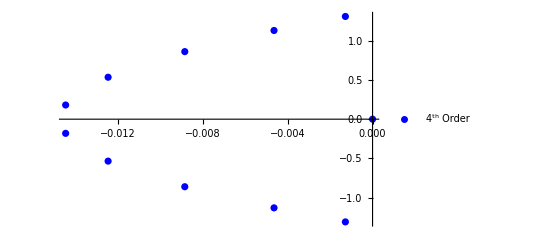

```mathematica
cplot4=ComplexListPlot[vals4,AspectRatio->1/GoldenRatio, PlotStyle->Blue, PlotLegends->{"4^th Order"},PlotRange->All]
```

#### Solve p=6

```mathematica
conds6b[n_]:=conds6b[n]=(Div6b[n].R26b[n].r[n]-R26b[n] .(3e[n]))//Simplify
conds6c[n_]:=conds6c[n]=(Div6c[n].R26c[n].r[n]-R26c[n] .(3e[n]))//Simplify
conds6b[n]//MatrixForm
conds6c[n]//MatrixForm
```

(-3 b[0]+b[2]
1/4 (-11 b[1]+3 b[3])
-3 b[2]+b[4]
-b[1]/4-3 b[3]+(5 b[5])/4
1/2 (-b[2]-6 b[4]+3 b[6])
-(3 b[3])/4-3 b[5]+(7 b[7])/4
-b[4]-3 b[6]+2 b[8]
-(5 b[5])/4-3 b[7]+(9 b[9])/4
1/2 (-3 b[6]-6 b[8]+5 b[10])
-(7 b[7])/4-3 b[9]
-2 b[8]-3 b[10])

(-3 c[0]+c[3]
1/3 (-9 c[1]+c[2]+2 c[4])
1/6 (c[1]-18 c[2]+5 c[5])
-3 c[3]+c[6]
-c[1]/6-3 c[4]+(7 c[7])/6
1/3 (-c[2]-9 c[5]+4 c[8])
1/2 (-c[3]-6 c[6]+3 c[9])
1/3 (-2 c[4]-9 c[7]+5 c[10])
-(5 c[5])/6-3 c[8]
-c[6]-3 c[9]
-(7 c[7])/6-3 c[10])

```mathematica
sol6b[n_]:=sol6b[n]=Solve[Join[conds6b[n][[1;;n-2]],Table[b[n-i]-((n-i)^2+q[i]),{i,1,2}],{q[1]-2,q[2]-2}]==0,Join[Table[b[i-1],{i,n}],{q[1],q[2]}]][[1]]
sol6b[n]//MatrixForm
sol6b[n+1]//MatrixForm
```

(b[0]→2
b[1]→3
b[2]→6
b[3]→11
b[4]→18
b[5]→27
b[6]→38
b[7]→51
b[8]→66
b[9]→83
b[10]→102
q[1]→2
q[2]→2)

(b[0]→2
b[1]→3
b[2]→6
b[3]→11
b[4]→18
b[5]→27
b[6]→38
b[7]→51
b[8]→66
b[9]→83
b[10]→102
b[11]→123
q[1]→2
q[2]→2)

```mathematica
Solve[(b[0]/.sol6b[n])==(b[0]/.sol6b[n+2])]
Solve[(b[0]/.sol6b[n+1])==(b[0]/.sol6b[n+3])]
```

{{}}

{{}}

```mathematica
R26b[n]/.sol6b[n]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 27 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 38 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 51 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 66 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 83 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 102)

```mathematica
SDiv6b[n_]:=SDiv6b[n]=Inverse[R26b[n]].Div6b[n].R26b[n]/.sol6b[n]
SDiv6b[n]//MatrixForm
```

(0 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | 0 | 11/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3/44 | 0 | 0 | 0 | 27/44 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/12 | 0 | 0 | 0 | 19/36 | 0 | 0 | 0 | 0
0 | 0 | 0 | -11/108 | 0 | 0 | 0 | 17/36 | 0 | 0 | 0
0 | 0 | 0 | 0 | -9/76 | 0 | 0 | 0 | 33/76 | 0 | 0
0 | 0 | 0 | 0 | 0 | -9/68 | 0 | 0 | 0 | 83/204 | 0
0 | 0 | 0 | 0 | 0 | 0 | -19/132 | 0 | 0 | 0 | 17/44
0 | 0 | 0 | 0 | 0 | 0 | 0 | -51/332 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -11/68 | 0 | 0)

```mathematica
SDiv6b[n].r[n]-3e[n]
```

{0,0,0,0,0,0,0,0,0,-1353/332,-73/17}

```mathematica
sol6c[n_]:=sol6c[n]=Solve[Join[conds6c[n][[1;;n-3]],Table[c[n-i]-((n-i)^2+q[i]),{i,1,3}],{q[1]-9/2,q[2]-9/2,q[3]-9/2}]==0,Join[Table[c[i-1],{i,n}],{q[1],q[2],q[3]}]][[1]]
sol6c[n]//MatrixForm
sol6c[n+1]//MatrixForm
sol6c[n+2]//MatrixForm
```

(c[0]→9/2
c[1]→11/2
c[2]→17/2
c[3]→27/2
c[4]→41/2
c[5]→59/2
c[6]→81/2
c[7]→107/2
c[8]→137/2
c[9]→171/2
c[10]→209/2
q[1]→9/2
q[2]→9/2
q[3]→9/2)

(c[0]→9/2
c[1]→11/2
c[2]→17/2
c[3]→27/2
c[4]→41/2
c[5]→59/2
c[6]→81/2
c[7]→107/2
c[8]→137/2
c[9]→171/2
c[10]→209/2
c[11]→251/2
q[1]→9/2
q[2]→9/2
q[3]→9/2)

(c[0]→9/2
c[1]→11/2
c[2]→17/2
c[3]→27/2
c[4]→41/2
c[5]→59/2
c[6]→81/2
c[7]→107/2
c[8]→137/2
c[9]→171/2
c[10]→209/2
c[11]→251/2
c[12]→297/2
q[1]→9/2
q[2]→9/2
q[3]→9/2)

```mathematica
Solve[(c[0]/.sol6c[n])==(c[0]/.sol6c[n+3])]
Solve[(c[0]/.sol6c[n+1])==(c[0]/.sol6c[n+4])]
Solve[(c[0]/.sol6c[n+2])==(c[0]/.sol6c[n+5])]
```

{{}}

{{}}

{{}}

```mathematica
R26c[n]/.sol6c[n]//MatrixForm
```

(9/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 17/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 27/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 41/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 59/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 81/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 107/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 171/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 209/2)

```mathematica
SDiv6c[n_]:=SDiv6c[n]=Inverse[R26c[n]].Div6c[n].R26c[n]/.sol6c[n]
SDiv6c[n]//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 17/66 | 0 | 41/66 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11/102 | 0 | 0 | 0 | 59/102 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | -11/246 | 0 | 0 | 0 | 0 | 0 | 107/246 | 0 | 0 | 0
0 | 0 | -17/354 | 0 | 0 | 0 | 0 | 0 | 137/354 | 0 | 0
0 | 0 | 0 | -1/18 | 0 | 0 | 0 | 0 | 0 | 19/54 | 0
0 | 0 | 0 | 0 | -41/642 | 0 | 0 | 0 | 0 | 0 | 209/642
0 | 0 | 0 | 0 | 0 | -59/822 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3/38 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -107/1254 | 0 | 0 | 0)

```mathematica
SDiv6c[n].r[n]-3e[n]
```

{0,0,0,0,0,0,0,0,-2761/822,-66/19,-4511/1254}

```mathematica
(* Div6 = 3/2 Div6a - 3/5 Div6b + 1/10 Div6c *)
(* Div6a = 2/3 Div6 + 2/5 Div6b - 1/15 Div6c *)
conds6a[n_]:=conds6a[n]=((2/3Div6[n].R26a[n]+2/5R26a[n].Inverse[R26b[n]].Div6b[n].R26b[n]-1/15R26a[n].Inverse[R26c[n]].Div6c[n].R26c[n]).r[n]-R26a[n] .(3e[n]))/.sol6b[n]/.sol6c[n]//Expand
conds6a[n]//MatrixForm
```

(-2 a[0]+a[1]-(2 a[2])/5+a[3]/15-2 a[0,1]-2 a[0,2]+9/5 a[1,2]
-(21 a[1])/10+(46 a[2])/45-(3 a[3])/10+(2 a[4])/45-2 a[0,1]-76/45 a[1,2]
-(22 a[1])/45-2 a[2]+(3 a[3])/2-(2 a[4])/5+a[5]/18-2 a[0,2]-134/45 a[1,2]
a[1]/10-a[2]-2 a[3]+2 a[4]-a[5]/2+a[6]/15-3/10 a[1,2]
-a[1]/90+a[2]/5-(3 a[3])/2-2 a[4]+(5 a[5])/2-(3 a[6])/5+(7 a[7])/90+7/90 a[1,2]
-a[2]/45+(3 a[3])/10-2 a[4]-2 a[5]+3 a[6]-(7 a[7])/10+(4 a[8])/45-1/90 a[1,2]
-a[3]/30+(2 a[4])/5-(5 a[5])/2-2 a[6]+(7 a[7])/2-(4 a[8])/5+a[9]/10
-(2 a[4])/45+a[5]/2-3 a[6]-2 a[7]+4 a[8]-(9 a[9])/10+a[10]/9
-a[5]/18+(3 a[6])/5-(7 a[7])/2-(21899 a[8])/12330+(9 a[9])/2-a[10]
-a[6]/15+(7 a[7])/10-4 a[8]-(10719 a[9])/3154+5 a[10]
-(7 a[7])/90+(4 a[8])/5-(9 a[9])/2-(222421 a[10])/63954)

```mathematica
sol6a[n_]:=sol6a[n]=Solve[Join[conds6a[n][[1;;n-3]],Table[a[n-i]-((n-i)^2+q[i]),{i,1,3}],{a[0]-1/2,(*a[1]-3/2,*)a[1,2],a[0,2],q[1]-a[0],q[2]-a[0],q[3]-a[0]}]==0,Join[Table[a[i-1],{i,n}],{a[0,1],a[1,2],a[0,2],q[1],q[2],q[3]}]][[1]]//Expand
sol6a[n]//MatrixForm
```

(a[0]→1/2
a[1]→37781908566907/28964322619098
a[2]→38449148342637/9654774206366
a[3]→87855925509157/9654774206366
a[4]→77817796511757/4827387103183
a[5]→730387659459763/28964322619098
a[6]→350425394074799/9654774206366
a[7]→1431155489091631/28964322619098
a[8]→129/2
a[9]→163/2
a[10]→201/2
a[0,1]→-1645850580127/4827387103183
a[1,2]→0
a[0,2]→0
q[1]→1/2
q[2]→1/2
q[3]→1/2)

```mathematica
R26a[n]/.sol6a[n]//N//MatrixForm
```

(0.5 | -0.34094 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.34094 | 1.30443 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 3.9824 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 9.09974 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 16.1201 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 25.2168 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 36.2956 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 49.411 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 64.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 81.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100.5)

```mathematica
SDiv6[n_]:=SDiv6[n]=Inverse[R26a[n]].Div6[n].R26a[n]/.sol6a[n]
SDiv6[n]//N//MatrixForm
```

(-1.21212 | 4.63752 | -0.96549 | -0.130052 | 0.170903 | 0. | 0. | 0. | 0. | 0. | 0.
-0.277606 | 1.06212 | 2.08827 | -1.0804 | 0.250635 | 0. | 0. | 0. | 0. | 0. | 0.
0.062782 | -0.240202 | 0. | 1.71374 | -0.607174 | 0.105534 | 0. | 0. | 0. | 0. | 0.
-0.00562006 | 0.0215022 | -0.328229 | 0. | 1.32861 | -0.415674 | 0.0664773 | 0. | 0. | 0. | 0.
0.000352501 | -0.00134866 | 0.0370569 | -0.423373 | 0. | 1.17323 | -0.337736 | 0.0510864 | 0. | 0. | 0.
0. | 0. | -0.00263211 | 0.054129 | -0.479444 | 0. | 1.07951 | -0.293917 | 0.0426303 | 0. | 0.
0. | 0. | 0. | -0.00417854 | 0.06662 | -0.521072 | 0. | 1.02101 | -0.266562 | 0.0374242 | 0.
0. | 0. | 0. | 0. | -0.00543741 | 0.0765522 | -0.550923 | 0. | 0.979033 | -0.247415 | 0.0338993
0. | 0. | 0. | 0. | 0. | -0.00651597 | 0.0844083 | -0.574546 | 0. | 0.947674 | -0.233721
0. | 0. | 0. | 0. | 0. | 0. | -0.0074224 | 0.0909404 | -0.593558 | 0. | 0.924847
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00819419 | 0.0962687 | -0.608209 | 0.)

```mathematica
SDiv6[n].r[n]-3e[n]
```

{0,0,0,0,0,0,0,0,-39915208368637097/112091928535909260,105185816517753/50278856090660,-67775612460495518/8732743269658047}

```mathematica
SDiv6[n].r[n]^3-5r[n]^2//N
```

{4.34,-0.361818,0.363491,-0.173072,0.0898061,-0.0577203,0.0270349,0.0207623,-42.518,245.534,-896.905}

#### Solve p=8

```mathematica
conds8b[n_]:=conds8b[n]=(Div8b[n].R28b[n].r[n]-R28b[n] .(3e[n]))//Simplify
conds8c[n_]:=conds8c[n]=(Div8c[n].R28c[n].r[n]-R28c[n] .(3e[n]))//Simplify
conds8d[n_]:=conds8d[n]=(Div8d[n].R28d[n].r[n]-R28d[n] .(3e[n]))//Simplify
conds8b[n]//MatrixForm
conds8c[n]//MatrixForm
conds8d[n]//MatrixForm
```

(-3 b[0]+b[2]
1/4 (-11 b[1]+3 b[3])
-3 b[2]+b[4]
-b[1]/4-3 b[3]+(5 b[5])/4
1/2 (-b[2]-6 b[4]+3 b[6])
-(3 b[3])/4-3 b[5]+(7 b[7])/4
-b[4]-3 b[6]+2 b[8]
-(5 b[5])/4-3 b[7]+(9 b[9])/4
1/2 (-3 b[6]-6 b[8]+5 b[10])
-(7 b[7])/4-3 b[9]
-2 b[8]-3 b[10])

(-3 c[0]+c[3]
1/3 (-9 c[1]+c[2]+2 c[4])
1/6 (c[1]-18 c[2]+5 c[5])
-3 c[3]+c[6]
-c[1]/6-3 c[4]+(7 c[7])/6
1/3 (-c[2]-9 c[5]+4 c[8])
1/2 (-c[3]-6 c[6]+3 c[9])
1/3 (-2 c[4]-9 c[7]+5 c[10])
-(5 c[5])/6-3 c[8]
-c[6]-3 c[9]
-(7 c[7])/6-3 c[10])

(-3 2[0]+2[4]
-3 2[1]+(3 2[3])/8+(5 2[5])/8
1/4 (-11 2[2]+3 2[6])
1/8 (2[1]-24 2[3]+7 2[7])
-3 2[4]+2[8]
-(2[1])/8-3 2[5]+(9 2[9])/8
-(2[2])/4-3 2[6]+(5 2[10])/4
-3/8 (2[3]+8 2[7])
-(2[4])/2-3 2[8]
-(5 2[5])/8-3 2[9]
-3/4 (2[6]+4 2[10]))

```mathematica
sol8b[n_]:=sol8b[n]=Solve[Join[conds8b[n][[1;;n-2]],Table[b[n-i]-((n-i)^2+q[i]),{i,1,2}],{q[1]-2,q[2]-2}]==0,Join[Table[b[i-1],{i,n}],{q[1],q[2]}]][[1]]
sol8b[n]//MatrixForm
sol8b[n+1]//MatrixForm
```

(b[0]→2
b[1]→3
b[2]→6
b[3]→11
b[4]→18
b[5]→27
b[6]→38
b[7]→51
b[8]→66
b[9]→83
b[10]→102
q[1]→2
q[2]→2)

(b[0]→2
b[1]→3
b[2]→6
b[3]→11
b[4]→18
b[5]→27
b[6]→38
b[7]→51
b[8]→66
b[9]→83
b[10]→102
b[11]→123
q[1]→2
q[2]→2)

```mathematica
Solve[(b[0]/.sol8b[n])==(b[0]/.sol8b[n+2])]
Solve[(b[0]/.sol8b[n+1])==(b[0]/.sol8b[n+3])]
```

{{}}

{{}}

```mathematica
R28b[n]/.sol8b[n]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 27 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 38 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 51 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 66 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 83 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 102)

```mathematica
SDiv8b[n_]:=SDiv8b[n]=Inverse[R28b[n]].Div8b[n].R28b[n]/.sol8b[n]
SDiv8b[n]//MatrixForm
```

(0 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | 0 | 11/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3/44 | 0 | 0 | 0 | 27/44 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/12 | 0 | 0 | 0 | 19/36 | 0 | 0 | 0 | 0
0 | 0 | 0 | -11/108 | 0 | 0 | 0 | 17/36 | 0 | 0 | 0
0 | 0 | 0 | 0 | -9/76 | 0 | 0 | 0 | 33/76 | 0 | 0
0 | 0 | 0 | 0 | 0 | -9/68 | 0 | 0 | 0 | 83/204 | 0
0 | 0 | 0 | 0 | 0 | 0 | -19/132 | 0 | 0 | 0 | 17/44
0 | 0 | 0 | 0 | 0 | 0 | 0 | -51/332 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -11/68 | 0 | 0)

```mathematica
SDiv8b[n].r[n]-3e[n]
```

{0,0,0,0,0,0,0,0,0,-1353/332,-73/17}

```mathematica
sol8c[n_]:=sol8c[n]=Solve[Join[conds8c[n][[1;;n-3]],Table[c[n-i]-((n-i)^2+q[i]),{i,1,3}],{q[1]-9/2,q[2]-9/2,q[3]-9/2}]==0,Join[Table[c[i-1],{i,n}],{q[1],q[2],q[3]}]][[1]]
sol8c[n]//MatrixForm
sol8c[n+1]//MatrixForm
sol8c[n+2]//MatrixForm
```

(c[0]→9/2
c[1]→11/2
c[2]→17/2
c[3]→27/2
c[4]→41/2
c[5]→59/2
c[6]→81/2
c[7]→107/2
c[8]→137/2
c[9]→171/2
c[10]→209/2
q[1]→9/2
q[2]→9/2
q[3]→9/2)

(c[0]→9/2
c[1]→11/2
c[2]→17/2
c[3]→27/2
c[4]→41/2
c[5]→59/2
c[6]→81/2
c[7]→107/2
c[8]→137/2
c[9]→171/2
c[10]→209/2
c[11]→251/2
q[1]→9/2
q[2]→9/2
q[3]→9/2)

(c[0]→9/2
c[1]→11/2
c[2]→17/2
c[3]→27/2
c[4]→41/2
c[5]→59/2
c[6]→81/2
c[7]→107/2
c[8]→137/2
c[9]→171/2
c[10]→209/2
c[11]→251/2
c[12]→297/2
q[1]→9/2
q[2]→9/2
q[3]→9/2)

```mathematica
Solve[(c[0]/.sol8c[n])==(c[0]/.sol8c[n+3])]
Solve[(c[0]/.sol8c[n+1])==(c[0]/.sol8c[n+4])]
Solve[(c[0]/.sol8c[n+2])==(c[0]/.sol8c[n+5])]
```

{{}}

{{}}

{{}}

```mathematica
R28c[n]/.sol8c[n]//MatrixForm
```

(9/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 17/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 27/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 41/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 59/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 81/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 107/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 171/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 209/2)

```mathematica
SDiv8c[n_]:=SDiv8c[n]=Inverse[R28c[n]].Div8c[n].R28c[n]/.sol8c[n]
SDiv8c[n]//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 17/66 | 0 | 41/66 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11/102 | 0 | 0 | 0 | 59/102 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | -11/246 | 0 | 0 | 0 | 0 | 0 | 107/246 | 0 | 0 | 0
0 | 0 | -17/354 | 0 | 0 | 0 | 0 | 0 | 137/354 | 0 | 0
0 | 0 | 0 | -1/18 | 0 | 0 | 0 | 0 | 0 | 19/54 | 0
0 | 0 | 0 | 0 | -41/642 | 0 | 0 | 0 | 0 | 0 | 209/642
0 | 0 | 0 | 0 | 0 | -59/822 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3/38 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -107/1254 | 0 | 0 | 0)

```mathematica
SDiv8c[n].r[n]-3e[n]
```

{0,0,0,0,0,0,0,0,-2761/822,-66/19,-4511/1254}

```mathematica
sol8d[n_]:=sol8d[n]=Solve[Join[conds8d[n][[1;;n-4]],Table[d[n-i]-((n-i)^2+q[i]),{i,1,4}],{q[1]-8,q[2]-8,q[3]-8,q[4]-8}]==0,Join[Table[d[i-1],{i,n}],{q[1],q[2],q[3],q[4]}]][[1]]
sol8d[n]//MatrixForm
sol8d[n+1]//MatrixForm
sol8d[n+2]//MatrixForm
sol8d[n+3]//MatrixForm
```

(2[0]→8
2[1]→9
2[2]→12
2[3]→17
2[4]→24
2[5]→33
2[6]→44
2[7]→57
2[8]→72
2[9]→89
2[10]→108
q[1]→8
q[2]→8
q[3]→8
q[4]→8)

(2[0]→8
2[1]→9
2[2]→12
2[3]→17
2[4]→24
2[5]→33
2[6]→44
2[7]→57
2[8]→72
2[9]→89
2[10]→108
2[11]→129
q[1]→8
q[2]→8
q[3]→8
q[4]→8)

(2[0]→8
2[1]→9
2[2]→12
2[3]→17
2[4]→24
2[5]→33
2[6]→44
2[7]→57
2[8]→72
2[9]→89
2[10]→108
2[11]→129
2[12]→152
q[1]→8
q[2]→8
q[3]→8
q[4]→8)

(2[0]→8
2[1]→9
2[2]→12
2[3]→17
2[4]→24
2[5]→33
2[6]→44
2[7]→57
2[8]→72
2[9]→89
2[10]→108
2[11]→129
2[12]→152
2[13]→177
q[1]→8
q[2]→8
q[3]→8
q[4]→8)

```mathematica
Solve[(d[0]/.sol8d[n])==(d[0]/.sol8d[n+4])]
Solve[(d[0]/.sol8d[n+1])==(d[0]/.sol8d[n+5])]
Solve[(d[0]/.sol8d[n+2])==(d[0]/.sol8d[n+6])]
Solve[(d[0]/.sol8d[n+3])==(d[0]/.sol8d[n+7])]
```

{{}}

{{}}

{{}}

«1 more identical outputs»

```mathematica
R28d[n]/.sol8d[n]//MatrixForm
```

(8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 33 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 44 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 57 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 72 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 89 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 108)

```mathematica
SDiv8d[n_]:=SDiv8d[n]=Inverse[R28d[n]].Div8d[n].R28d[n]/.sol8d[n]
SDiv8d[n]//MatrixForm
```

(0 | 0 | 0 | 0 | 3/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 17/72 | 0 | 11/24 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/8 | 0 | 0 | 0 | 11/24 | 0 | 0 | 0 | 0
0 | 9/136 | 0 | 0 | 0 | 0 | 0 | 57/136 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/8 | 0 | 0
0 | -3/88 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 89/264 | 0
0 | 0 | -3/88 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27/88
0 | 0 | 0 | -17/456 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/24 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -33/712 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -11/216 | 0 | 0 | 0 | 0)

```mathematica
SDiv8d[n].r[n]-3e[n]
```

{0,0,0,0,0,0,0,-473/152,-19/6,-2301/712,-119/36}

```mathematica
(* Div8 = 8/5 Div8a - 4/5 Div8b + 8/35 Div8c - 1/35 Div8d *)
(* Div8a = 5/8 Div8 + 1/2 Div8b - 1/7 Div8c + 1/56 Div8d *)
conds8a[n_]:=conds8a[n]=((5/8Div8[n].R28a[n]+1/2R28a[n].Inverse[R28b[n]].Div8b[n].R28b[n]-1/7R28a[n].Inverse[R28c[n]].Div8c[n].R28c[n]+1/56R28a[n].Inverse[R28d[n]].Div8d[n].R28d[n]).r[n]-R26a[n] .(3e[n]))/.sol8b[n]/.sol8c[n]/.sol8d[n]//Expand
conds8a[n]//MatrixForm
```

(-(15 a[0])/8+a[1]-a[2]/2+a[3]/7-a[4]/56-15/8 a[0,1]-15/8 a[0,2]+7/4 a[1,2]
-2 a[1]+(22 a[2])/21-(171 a[3])/448+(2 a[4])/21-(5 a[5])/448-15/8 a[0,1]-269/168 a[1,2]
-(10 a[1])/21-(421 a[2])/224+(3 a[3])/2-a[4]/2+(5 a[5])/42-(3 a[6])/224-15/8 a[0,2]-(3803 a[1,2])/1344
(55 a[1])/448-a[2]-(15 a[3])/8+2 a[4]-(5 a[5])/8+a[6]/7-a[7]/64-57/224 a[1,2]
-a[1]/42+a[2]/4-(3 a[3])/2-(15 a[4])/8+(5 a[5])/2-(3 a[6])/4+a[7]/6-a[8]/56+13/168 a[1,2]
a[1]/448-a[2]/21+(3 a[3])/8-2 a[4]-(15 a[5])/8+3 a[6]-(7 a[7])/8+(4 a[8])/21-(9 a[9])/448-13/672 a[1,2]
a[2]/224-a[3]/14+a[4]/2-(5 a[5])/2-(15 a[6])/8+(7 a[7])/2-a[8]+(3 a[9])/14-(5 a[10])/224+1/448 a[1,2]
(3 a[3])/448-(2 a[4])/21+(5 a[5])/8-3 a[6]-(16433 a[7])/8512+4 a[8]-(9 a[9])/8+(5 a[10])/21
a[4]/112-(5 a[5])/42+(3 a[6])/4-(7 a[7])/2-(22275 a[8])/15344+(9 a[9])/2-(5 a[10])/4
(5 a[5])/448-a[6]/7+(7 a[7])/8-4 a[8]-(218446197 a[9])/62878144+5 a[10]
(3 a[6])/224-a[7]/6+a[8]-(9 a[9])/2-(25551227 a[10])/7162848)

```mathematica
sol8a[n_]:=sol8a[n]=Solve[Join[conds8a[n][[1;;n-4]],Table[a[n-i]-((n-i)^2+q[i]),{i,1,4}],{a[0]-1/2,(*a[1]-3/2,*)a[1,2],a[0,2],q[1]-a[0],q[2]-a[0],q[3]-a[0],q[4]-a[0]}]==0,Join[Table[a[i-1],{i,n}],{a[0,1],a[1,2],a[0,2],q[1],q[2],q[3],q[4]}]][[1]]//Expand
sol8a[n]//MatrixForm
```

(a[0]→1/2
a[1]→3000475508386005/2318924091935434
a[2]→9265791080247657/2318924091935434
a[3]→338446547739688611/37102785470966944
a[4]→74938937172914163/4637848183870868
a[5]→4689764097615190431/185513927354834720
a[6]→84367651458853461/2318924091935434
a[7]→99/2
a[8]→129/2
a[9]→163/2
a[10]→201/2
a[0,1]→-3876439586692437/11594620459677170
a[1,2]→0
a[0,2]→0
q[1]→1/2
q[2]→1/2
q[3]→1/2
q[4]→1/2)

```mathematica
R28a[n]/.sol8a[n]//N//MatrixForm
```

(0.5 | -0.334331 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.334331 | 1.29391 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 3.99573 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 9.12186 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 16.1581 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 25.2798 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 36.3822 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 49.5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 64.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 81.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100.5)

```mathematica
SDiv8[n_]:=SDiv8[n]=Inverse[R28a[n]].Div8[n].R28a[n]/.sol8a[n]
SDiv8[n]//N//MatrixForm
```

(-1.25154 | 4.84363 | -1.77219 | 0.520256 | 0.105498 | -0.0564021 | 0. | 0. | 0. | 0. | 0.
-0.271705 | 1.05154 | 2.13022 | -1.30072 | 0.502987 | -0.0843507 | 0. | 0. | 0. | 0. | 0.
0.0637501 | -0.246722 | -0.00357143 | 1.82632 | -0.80877 | 0.241018 | -0.0325189 | 0. | 0. | 0. | 0.
-0.00719942 | 0.0278628 | -0.350431 | 0. | 1.41709 | -0.554269 | 0.151942 | -0.0193804 | 0. | 0. | 0.
0.000788236 | -0.00305059 | 0.0494578 | -0.45163 | 0. | 1.25162 | -0.450327 | 0.116704 | -0.0142564 | 0. | 0.
-0.0000472328 | 0.000182798 | -0.00602133 | 0.0721671 | -0.511336 | 0. | 1.15134 | -0.391616 | 0.0971977 | -0.011514 | 0.
0. | 0. | 0.000392237 | -0.00955135 | 0.0888243 | -0.555872 | 0. | 1.08844 | -0.354569 | 0.0853373 | -0.00986549
0. | 0. | 0. | 0.000658143 | -0.0124353 | 0.102141 | -0.587996 | 0. | 1.04242 | -0.329293 | 0.0773449
0. | 0. | 0. | 0. | 0.000894691 | -0.0149309 | 0.112813 | -0.613953 | 0. | 1.01085 | -0.311628
0. | 0. | 0. | 0. | 0. | 0.00110779 | -0.017006 | 0.121472 | -0.633129 | 0. | 0.986503
0. | 0. | 0. | 0. | 0. | 0. | 0.0012929 | -0.0187633 | 0.128358 | -0.648756 | 0.)

```mathematica
SDiv8[n].r[n]-3e[n]
```

{0,0,0,0,0,0,0,14427791717854014011/171414868875867281280,-495909402456311213/697996151672565634,308896250612547145641/120955080635352237440,-17260966093900760955/2175150798235437092}

```mathematica
SDiv8[n].r[n]^3-5r[n]^2//N
```

{4.41462,-0.378883,0.377303,-0.193619,0.110831,-0.0876286,0.0882448,10.994,-82.7438,295.471,-913.38}

### Banded matrices

```mathematica
mconds2[n_]:=Module[{conds},
conds=Join[conds2[n][[1;;n-1]],Table[a[n-i]-((n-i)^2+1/2),{i,1,1}]];
Table[D[conds[[i]],a[j-1]],{i,n},{j,n}]
]
mconds2[n]//MatrixForm
```

Part::take: Cannot take positions 1 through 10 in conds2[11].

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Part::partw: Part 3 of Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {1}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],3]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],4]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],5]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],6]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],7]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],8]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],9]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],10]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1})[conds2[11]⟦1;;10⟧,{-201/2+a[10]}] Part^(1,0)[Join[conds2[11]⟦1;;10⟧,{-201/2+a[10]}],11])

```mathematica
mconds4w[n_]:=Module[{conds},
conds=Join[conds4w[n][[1;;n-2]],Reverse[Table[b[n-i]-((n-i)^2+2),{i,1,2}]]];
Table[D[conds[[i]],b[j-1]],{i,n},{j,n}]
]
mconds4w[n]//MatrixForm
```

Part::take: Cannot take positions 1 through 9 in conds4w[11].

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Part::partw: Part 3 of Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {1,0} | {0,1}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],3] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],3]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],4] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],4]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],5] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],5]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],6] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],6]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],7] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],7]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],8] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],8]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],9] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],9]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],10] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],10]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],11] | Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],11])

```mathematica
({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {1,0}, {0,1}}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],3], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],3]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],4], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],4]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],5], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],5]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],6], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],6]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],7], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],7]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],8], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],8]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],9], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],9]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],10], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],10]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[0,{1,0}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],11], Derivative[0,{0,1}][Join][conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Derivative[1,0][Part][Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],11]}})
```

Part::take: Cannot take positions 1 through 9 in conds4w[11].

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 9 in conds4w[11].

General::stop: Further output of Part::take will be suppressed during this calculation.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

{{0,0,0,0,0,0,0,0,0,0,0},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,1}},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],3],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],3]},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],4],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],4]},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],5],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],5]},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],6],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],6]},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],7],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],7]},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],8],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],8]},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],9],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],9]},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],10],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],10]},{0,0,0,0,0,0,0,0,0,Join^(0,{1,0})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],11],Join^(0,{0,1})[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}] Part^(1,0)[Join[conds4w[11]⟦1;;9⟧,{-83+b[9],-102+b[10]}],11]}}

```mathematica
mconds4n[n_]:=Module[{conds,vars,mat,rhs},
conds=Join[{a[0]-1/2},conds4n[n][[1;;n-2]],Reverse[Table[a[n-i]-((n-i)^2+1/2),{i,1,2}]]]/.{a[0,2]->0,a[1,2]->0};
vars=Join[{a[0],a[0,1],a[1]},Table[a[i-1],{i,3,n}]];
mat=Table[D[conds[[i]],vars[[j]]],{i,n+1},{j,n+1}];
rhs=Table[conds[[i]]-Sum[mat[[i,j]]vars[[j]],{j,n+1}],{i,n+1}];
{mat,rhs}
]
{mat,rhs}=mconds4n[n];
mat//MatrixForm
rhs//MatrixForm
```

Part::take: Cannot take positions 1 through 9 in conds4n[11].

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 4 of Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

({1} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {1,0} | {0,1}
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] | Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}])

({-1/2}
conds4n[11]⟦1;;9⟧
{-163/2,-201/2}
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦4⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦5⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦6⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦7⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦8⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦9⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦10⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦11⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]
Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦12⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}])

```mathematica
({{{1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {1,0}, {0,1}}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], 0, 0, 0, 0, 0, 0, 0, 0, 0, Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}], Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}})
```

Part::take: Cannot take positions 1 through 9 in conds4n[11].

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 9 in conds4n[11].

General::stop: Further output of Part::take will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

{{{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}},{0,0,0,0,0,0,0,0,0,0,0,0},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,1}},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]},{Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],0,0,0,0,0,0,0,0,0,Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}}

```mathematica
({{{-1/2}}, {conds4n[11]⟦1;;9⟧}, {{-163/2,-201/2}}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦4⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦5⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦6⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦7⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦8⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦9⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦10⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦11⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}, {Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦12⟧-a[10] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Derivative[{0},0,{0,1}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Derivative[{0},0,{1,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Derivative[1,0][Part][Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Derivative[{1},0,{0,0}][Join][{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}})
```

Part::take: Cannot take positions 1 through 9 in conds4n[11].

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 4 of Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] does not exist.

Part::take: Cannot take positions 1 through 9 in conds4n[11].

General::stop: Further output of Part::take will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::partw: Part 5 of Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] does not exist.

Part::partw: Part 6 of Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-1/2},conds4n[11]⟦1;;9⟧,{-163/2,-201/2},Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦4⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],4] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦5⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],5] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦6⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],6] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦7⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],7] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦8⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],8] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦9⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],9] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦10⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],10] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦11⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],11] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]⟦12⟧-a[10] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({0},0,{0,1})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[9] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({0},0,{1,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]-a[0] Part^(1,0)[Join[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}],12] Join^({1},0,{0,0})[{-1/2+a[0]},conds4n[11]⟦1;;9⟧,{-163/2+a[9],-201/2+a[10]}]}